```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
rho=Flatten[Import["./kappa.dat"]];
lam1=Flatten[Import["./lam1.dat"]];
lam2=Flatten[Import["./lam2.dat"]];
lam3=Flatten[Import["./lam3.dat"]];
k=Flatten[Import["./k1.dat"]];
rhobar=rho/k;
lam1bar=lam1/k^2;
lam2bar=lam2;
lam3bar=lam3*k^2;
```

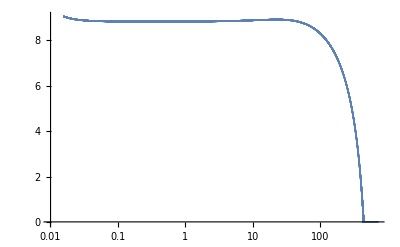

```mathematica
ListPlot[Transpose[{k,rhobar}],PlotRange->All,ScalingFunctions->{"Log",Automatic}]
```

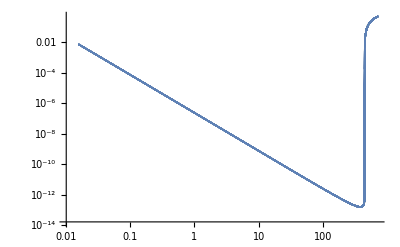

```mathematica
ListPlot[Transpose[{k,lam1bar}],PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

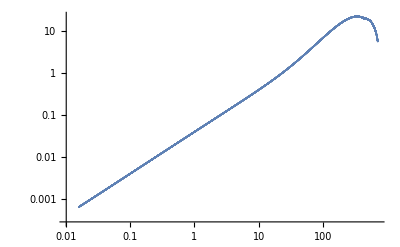

```mathematica
ListPlot[Transpose[{k,lam2bar}],PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

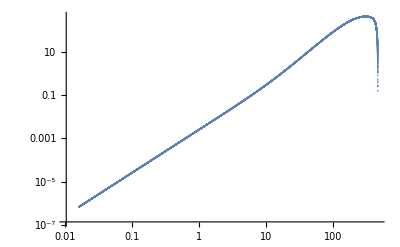

```mathematica
ListPlot[Transpose[{k,lam3bar}],PlotRange->All,ScalingFunctions->{"Log","Log"}]
```